```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
data=RandomVariate[MultinomialDistribution[10,{0.3,0.25,0.45}],{3}]
```

{{4,2,4},{5,2,3},{2,2,6}}

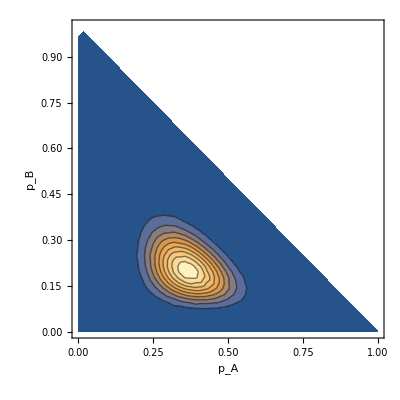

```mathematica
gFinal=ContourPlot[Likelihood[MultinomialDistribution[10,{p1,p2,1-p1-p2}],data],{p1,0,1},{p2,0,1},PlotRange->Full,Frame->{True,True,False,False},FrameLabel->{"p_A","p_B"}]
```

```mathematica
Export["Distributions_multinomialLikelihood.pdf",gFinal]
```

Distributions_multinomialLikelihood.pdf